```mathematica
a=2;b=3;n=20;
```

```mathematica
m=n/2;
```

```mathematica
h=(b-a)/(2m)//N;
```

```mathematica
f[x_]=E^(-x^2/3);
```

```mathematica
prib=h/3(f[a]+2Sum[f[a+2*i*h],{i,1,m-1}]+4Sum[f[a+(2*i-1)*h],{i,1,m}]+f[b])
```

0.135332

```mathematica
cetvrti[x_]=D[f[x],{x,4}]
```

4/3 ⅇ^(-x^2/3)-16/9 ⅇ^(-x^2/3) x^2+16/81 ⅇ^(-x^2/3) x^4

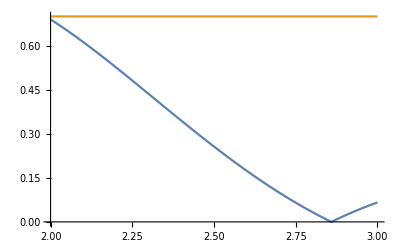

```mathematica
Plot[{Abs[cetvrti[x]],0.7},{x,2,3}]
```

```mathematica
m4=0.7;
```

```mathematica
greska=(b-a)/180*m4*h^4
```

2.43056×10^-8

```mathematica
njutn[f_,x_,x0_,eps_]:=Module[{},
iter[0]=x0//N;
izvod=D[f,x];
i=0;
While[Abs[f/.x->iter[i]]>=eps,
iter[i+1]=iter[i]-(f/.x->iter[i])/(izvod/.x->iter[i]);
i=i+1;
];
iter[i]
]
```

```mathematica
f[x_]=3 x^5+5 x^2-17;
```

```mathematica
njutn[f[x],x,2,10^-5]
```

1.25066

```mathematica
a=({{25, -1, 2, -1}, {0, 27, 3, 1}, {-1, -1, 20, 3}, {1, 1, -2, 22}});b=({{2}, {1}, {-1}, {0}});x0=({{1}, {-1}, {-1}, {1}});
```

```mathematica
jakobi[a_,b_,x0_,kmax_]:=Module[{},
res={x0};
n=Length[x0];
itnew=x0//N;
Do[
itold=itnew;
Do[
itnew[[i,1]]=-1/a[[i,i]](Sum[a[[i,j]]*itold[[j,1]],{j,1,i-1}]+Sum[a[[i,j]]*itold[[j,1]],{j,i+1,n}]-b[[i,1]]),
{i,1,n}];
res=Append[res,itnew],
{k,1,kmax}];
res
]
```

```mathematica
jakobi[a,b,x0,9]
```

{{{1},{-1},{-1},{1}},{{0.16},{0.111111},{-0.2},{-0.0909091}},{{0.0968081},{0.0626263},{-0.0228081},{-0.0305051}},{{0.0831095},{0.0407011},{-0.0374525},{-0.00932048}},{{0.0842514},{0.0415436},{-0.0424114},{-0.00903253}},{{0.0846934},{0.042084},{-0.0423554},{-0.00957354}},{{0.0846888},{0.0420978},{-0.0422251},{-0.00961309}},{{0.0846774},{0.0420848},{-0.0422187},{-0.00960167}},{{0.0846768},{0.0420836},{-0.0422216},{-0.00959998}},{{0.0846771},{0.0420839},{-0.042222},{-0.00960017}}}

```mathematica
ok[f_,t_,y_,a_,b_,t0_,y0_,n_]:=Module[{},
ttac[0]=t0;
wit[0]=y0;
h=(b-a)/n//N;
Do[
ttac[i+1]=ttac[i]+h;
wit[i+1]=wit[i]+h*f/.{t->ttac[i],y->wit[i]},
{i,0,n-1}];
Table[{ttac[i],wit[i]},{i,0,n}]
]
```

```mathematica
f[t_,y_]=y+15Cos[t]
```

y+15 Cos[t]

```mathematica
ok[f[t,y],t,y,0,1,0,3,20]
```

{{0,3},{0.05,3.9},{0.1,4.84406},{0.15,5.83252},{0.2,6.86572},{0.25,7.94406},{0.3,9.06795},{0.35,10.2378},{0.4,11.4543},{0.45,12.7178},{0.5,14.029},{0.55,15.3886},{0.6,16.7975},{0.65,18.2563},{0.7,19.7662},{0.75,21.3282},{0.8,22.9433},{0.85,24.613},{0.9,26.3387},{0.95,28.1218},{1.,29.9642}}